```mathematica
Quit[];
```

```mathematica
Needs["MyStyle`"]
```

### PlotStyles

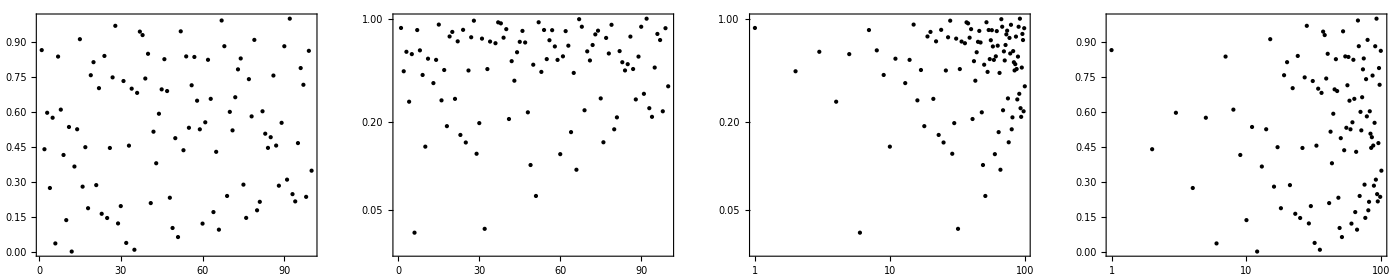

```mathematica
rndDat=RandomReal[{0,1},100];
GraphicsRow[{ListPlot[rndDat],
ListLogPlot[rndDat],
ListLogLogPlot[rndDat],
ListLogLinearPlot[rndDat]},ImageSize->4*350]
```

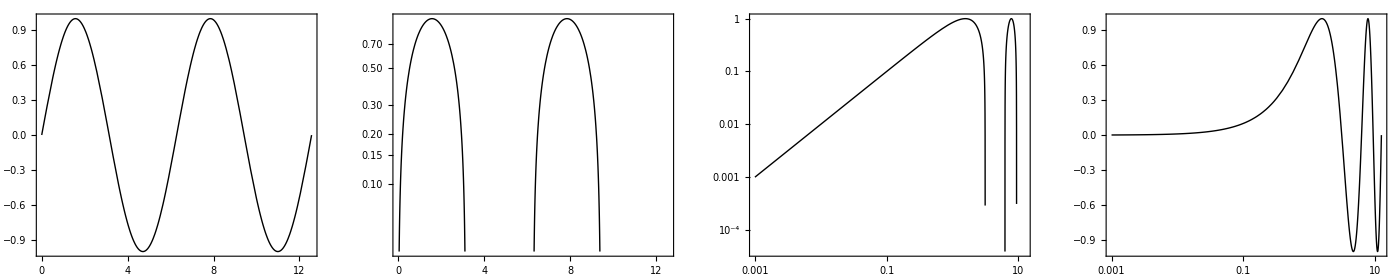

```mathematica
args=Sequence[Sin[x],{x,0.001,4Pi}];
GraphicsRow[{Plot[Evaluate[args]],
LogPlot[Evaluate[args]],
LogLogPlot[Evaluate[args]],
LogLinearPlot[Evaluate[args]]},ImageSize->4*350]
```

### errorListPlotBand

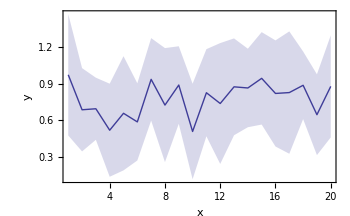

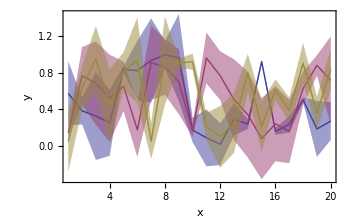

```mathematica
errorListPlotBand[RandomReal[{0.5,1},{20,2}],FrameLabel->{"x","y"}]
errorListPlotBand[Sequence@@RandomReal[{0,1},{3,20,2}],FrameLabel->{"x","y"}]
```

### Power spectra

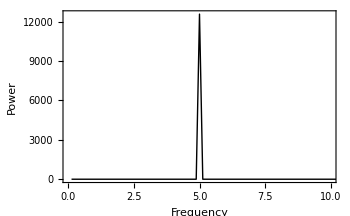

```mathematica
data=Table[Sin[5*p],{p,0,16Pi,.001}];
ListPlot[powerSpectrum[data,16Pi],Joined->True,FrameLabel->{"Frequency","Power"},PlotRange->{{0,10},All}]
```

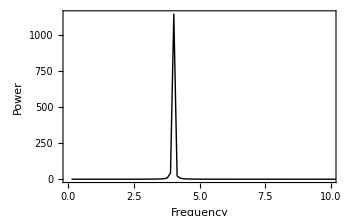

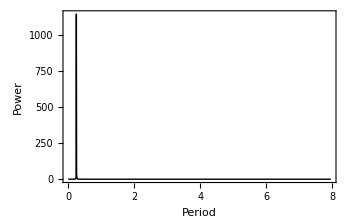

```mathematica
data=Table[Sin[4*p],{p,0,50,.01}];
ListPlot[powerSpectrum[data,50.],Joined->True,FrameLabel->{"Frequency","Power"},PlotRange->{{0,10},All}]
ListPlot[{1/#[[1]],#[[2]]}&/@powerSpectrum[data,50.],Joined->True,FrameLabel->{"Period","Power"},PlotRange->{All,All}]
```